```mathematica
n = 200
```

200

```mathematica
m0 = 5.0
```

5.

```mathematica
m[k_]  := m0 Exp[ (ⅈ 2 π k)/n]
```

```mathematica
mm = Array[m, n, 0];
```

```mathematica
F1[x_] :=( 1/n∑_(k=0)^(n-1) Log [ (x - mm[[k+1]])  Conjugate[ x - mm[[k+1]]]] ) /Log[m0 Conjugate[m0]]
```

```mathematica
F2[x_] := ( 1/n∑_(k=0)^(n-1) Log [ (x - mm[[k+1]])  Conjugate[ x - mm[[k+1]]]] ) /Log[x Conjugate[x]]
```

```mathematica
F11[x_] := Log[m0 Conjugate[m0]]
```

```mathematica
F11[1.0]
```

3.21888

```mathematica
F2[7.0] // N
```

1.+0. ⅈ

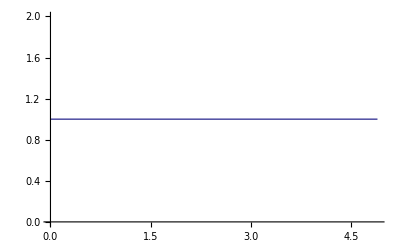

```mathematica
Plot[F1[x], {x, 0.001, 4.9}, PlotRange-> {0.,2.0}]
```

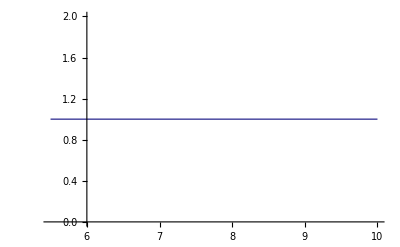

```mathematica
Plot[F2[x],{x,5.5,10.0}, PlotRange-> {0.,2.}]
```

```mathematica
DD = 50.0
```

50.

```mathematica
F3[sig_] := 1/n∑_(k=0)^(n-1) Log [ DD + (sig - mm[[k+1]])Conjugate[sig - mm[[k+1]]] ]
```

```mathematica
F33[sig_] := Log [ DD + sig Conjugate[sig]]
```

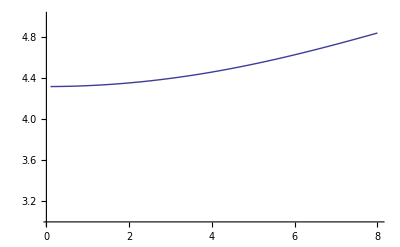

```mathematica
Plot[F3[sig],{sig, 0.1,8.0},PlotRange->{3.,5.0}]
```

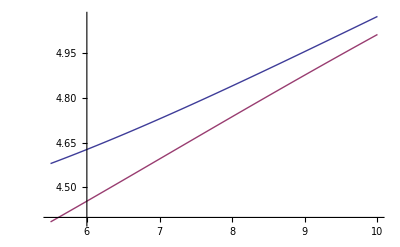

```mathematica
Plot[{F3[sig],F33[sig]},{sig, 5.5,10.0}]
```

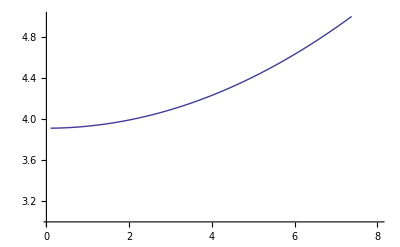

```mathematica
Plot[ (sig Conjugate[sig])/DD + Log[DD], {sig,0.1,8.0}, PlotRange->{3.,5.0}]
```

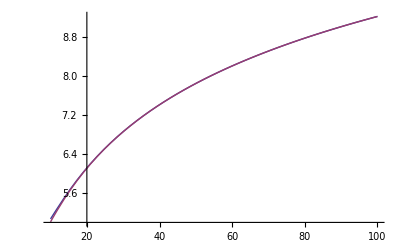

```mathematica
Plot[{F3[sig],F33[sig]},{sig, 10.,100.0}]
```

```mathematica
F3[0] - F33[0]
```

0.405465+0. ⅈ

```mathematica
A = 0.4054651081081704+0. ⅈ
```

0.405465+0. ⅈ